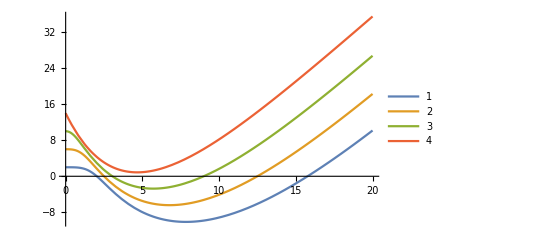

```mathematica
time=20;

{car4,car3,car2,car1}=NDSolveValue[{
x4''[t]==4*(3-x4'[t])/(15+0.5),
x3''[t]==4*(x4'[t]-x3'[t])/(Abs[x4[t]-x3[t]]+0.5),
x2''[t]==4*(x3'[t]-x2'[t])/(Abs[x3[t]-x2[t]]+0.5),
x1''[t]==4*(x2'[t]-x1'[t])/(Abs[x2[t]-x1[t]]+0.5),
x1[0]==2,x1'[0]==0,x2[0]==6,x2'[0]==0,x3[0]==10,x3'[0]==0,x4[0]==14,x4'[0]==-7},{x4,x3,x2,x1},{t,0,time},Method->{"DoubleStep", Method->"LinearlyImplicitMidpoint"}];
Plot[{car1[t],car2[t],car3[t],car4[t]},{t,0,time},PlotLegends->{"1","2","3","4"}]
```

```mathematica
c1pl={};
c2pl={};
c3pl={};
c4pl={};
i=0;
Do[ 
{
i=i+1,
If[t≥0,AppendTo[c1pl,{car1[t],0}],AppendTo[c1pl,{2,0}]],
If[t≥0,AppendTo[c2pl,{car2[t],0}],AppendTo[c2pl,{6,0}]],
If[t≥0,AppendTo[c3pl,{car3[t],0}],AppendTo[c3pl,{10,0}]],
If[t≥0,AppendTo[c4pl,{car4[t],0}],AppendTo[c4pl,{14,0}]],

If[Mod[i,2]==0,Subscript[pl, i]=Show[ListPlot[{Table[{2n,0.5},{n,-7,20}],Table[{2n,-0.5},{n,-7,20}]},PlotRange->{{-7,20},{-1,1}},PlotStyle->White,AspectRatio->1,Axes->False,Background->Black],ListPlot[{c1pl,c2pl,c3pl,c4pl},PlotRange->{{-7,20},{-1,1}},PlotStyle->PointSize[0.04],AspectRatio->1,Axes->False,Background->Black]
],
Subscript[pl, i]=Show[ListPlot[{Table[{2n+1,0.5},{n,-7,20}],Table[{2n+1,-0.5},{n,-7,20}]},PlotRange->{{-7,20},{-1,1}},PlotStyle->White,AspectRatio->1,Axes->False,Background->Black],ListPlot[{c1pl,c2pl,c3pl,c4pl},PlotRange->{{-7,20},{-1,1}},PlotStyle->PointSize[0.04],AspectRatio->1,Axes->False,Background->Black]]],
c1pl=Drop[c1pl,1],
c2pl=Drop[c2pl,1],
c3pl=Drop[c3pl,1],
c4pl=Drop[c4pl,1]
}
,{t,-1,time,0.15}]
gif=Table[Subscript[pl, t],{t,1,i}];
Export["E:\\test_gif(5).gif",gif];
SystemOpen["E:\\test_gif(5).gif"];
```